# Zestaw 8

## Zadanie 1. Moment bezwładności względem dowolnej osi, MomentOfInertia, Cylinder, Volume

Rozważyć jednorodny walec o masie , wysokości  oraz promieniu .
Dla ustalenia orientacji przestrzennej walca przyjąć, że jego środek masy jest w punkcie ,
a oś symetrii obrotowej jest zadana przez punkty  . 
W celu obliczenie momentu bezwładności zadanego walca względem dowolnej osi wykonaj następujące polecenia:

### 1) Sparametryzuj zadany walec jako obszar reg przy użyciu funkcji Cylinder

```mathematica
?Cylinder
```

```mathematica
centerOfMass = {xCm, yCm, zCm} = {0, 0, 0};

GetLineOfSymmetryPoints[l_] := {
{xCm, yCm, zCm -l/2}, {xCm, yCm, zCm + l/2}
}

GetCylinder[l_, r_] := Cylinder[
GetLineOfSymmetryPoints[l],
r
]

reg = GetCylinder[l, r]
```

Cylinder[{{0,0,-l/2},{0,0,l/2}},r]

### 2) Przedstaw ten obszar używając Graphics3D

Na potrzeby rysunku podstaw .
Na rysunku nanieś oś symetrii obrotowej walca, przykładowo korzystając z InfiniteLine.

```mathematica
?InfiniteLine
```

```mathematica
l1 = 4;
r1 = 1;

Graphics3D[{
GetCylinder[l1, r1],
InfiniteLine[GetLineOfSymmetryPoints[l1]]
}]
```

-Graphics3D-

### 3) Wyznacz tensor momentu bezwładności IM (macierz ) korzystając z funkcji MomentOfInertia

Tensor momentu bezwładności mówi nam, jak trudno rozkręcić bryłę wokół dowolnej osi, nie tylko jednej.
W konkretnym układzie współrzędnych ten tensor zapisujemy w postaci macierzy momentu bezwładności.
Więcej na https://en.wikipedia.org/wiki/Moment_of_inertia#Inertia_tensor.

```mathematica
?MomentOfInertia
```

```mathematica
IM = MomentOfInertia[reg]
```

{{(π r^2 (l^4+3 l^2 r^2))/(12 √(l^2)),0,0},{0,(π r^2 (l^4+3 l^2 r^2))/(12 √(l^2)),0},{0,0,1/2 √(l^2) π r^4}}

Uprość uzyskane wyrażenie korzystając z funkcji Simplify oraz opcji Assumptions -> l > 0 && r > 0 .

```mathematica
assumptions = Assumptions -> l > 0 && r > 0;

IM = Simplify[
MomentOfInertia[reg],
assumptions
]
```

{{1/12 l π r^2 (l^2+3 r^2),0,0},{0,1/12 l π r^2 (l^2+3 r^2),0},{0,0,1/2 l π r^4}}

### 4) Uzyskany tensor momentu bezwładności zawiera objętość walca, a chcemy by zamiast tej objętości występowała masa

W tym celu wyznacz objętość walca :

#### i) z pamięci

```mathematica
V = π r^2 * l
```

l π r^2

#### ii) licząc jako całkę po obszarze reg

```mathematica
V = Simplify[
Integrate[1, {x, y, z} ∈ reg], 
assumptions
]
```

l π r^2

#### iii) używając funkcji Volume

```mathematica
V = Simplify[
Volume[reg],
assumptions
]
```

l π r^2

Następnie zdefiniuj tensor momentu bezwładności jako .

```mathematica
fIM[l_, r_, m_] := m IM / V

fIM[l, r, m]
```

{{1/12 m (l^2+3 r^2),0,0},{0,1/12 m (l^2+3 r^2),0},{0,0,(m r^2)/2}}

### 5) Oblicz moment bezwładności zadanego walca względem dowolnej osi obrotu przechodzącej przez jego środek masy

Korzystając z parametryzacji  jako wektora jednostkowego, oblicz moment bezwładności zadanego walca względem dowolnej osi obrotu przechodzącej przez jego środek masy.

```mathematica
u[θ_, ϕ_] := {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]}
```

Szukany moment bezwładności dla osi równoległej do wektora  będzie się wyrażał jako .
Wyraź znaleziony moment bezwładności jako funkcję zależną od  oraz (l, r, m).

```mathematica
IMu[θ_, ϕ_][l_, r_, m_] := u[θ, ϕ] . fIM[l, r, m] . u[θ, ϕ]

IMu[θ, ϕ][l, r, m]
```

1/2 m r^2 Cos[θ]^2+1/12 m (l^2+3 r^2) Cos[ϕ]^2 Sin[θ]^2+1/12 m (l^2+3 r^2) Sin[θ]^2 Sin[ϕ]^2

Zauważ, że   jest wielkością skalarną, w tym wyrażeniu  to iloczyn skalarny; równoważnie można zapisać , jeśli mnożymy macierzowo.

### 6) Oblicz moment bezwładności walca względem wektorów , oraz

```mathematica
momentsOfInertia = Map[
axis |-> Module[{axisName, vector},
{axisName, vector} = axis;
axisName -> Simplify[
vector . fIM[l, r, m].  vector,
assumptions
]
],
{
{"x", {1, 0, 0}},
{"y", {0, 1, 0}},
{"z", {0, 0, 1}}
}
]
```

{x→1/12 m (l^2+3 r^2),y→1/12 m (l^2+3 r^2),z→(m r^2)/2}

Sprawdź czy wynik zgadza się z wartościami dla tych momentów bezwładności, np. porównując z wartościami znalezionymi w Wikipedii.
Odp: Wynik zgadza się

### 7) Znając moment bezwładności dla walca, oblicz moment bezwładności jednorodnego dysku o promieniu i masie względem osi oraz

Przejdź do granicy  dla momentów bezwładności obliczonych w punkcie 6).

```mathematica
selectedMomentsOfInertia = Select[
moment |-> Module[{axisName, value},
{axisName, value} = List @@ moment;
axisName === "x" || axisName === "z"
]
][momentsOfInertia];

Map[
moment |-> Module[{axisName, value, f},
{axisName, value} = List @@ moment;
axisName -> (value /. l -> 0)
],
selectedMomentsOfInertia
]
```

{x→(m r^2)/4,z→(m r^2)/2}

## Zadanie 2. Moment bezwładności niejednorodnej bryły, Integrate, Ball, Assumptions

Wyznaczyć moment bezwładności niejednorodnej kuli o masie  oraz promieniu  względem dowolnej (wybranej) osi przechodzącej przez środek masy tej kuli.

Wskazówka nr 1: zmiana funkcji gęstości przy zachowaniu całkowitej masy kuli  oraz zachowanym promieniu  wymusza zmianę gęstości materiału  z którego wykonana jest kula.
Wskazówka nr 2: sposób obliczenia momentu bezwładności dla niejednorodnej bryły jest opisany m.in. w materiałach dotyczących funkcji MomentOfInertia.
Do zdefiniowania obszaru całkowania użyj funkcji Ball.

```mathematica
?Ball
```

Obliczenia wykonać dla rozkładu masy zadanego przez funkcję gęstości:

### 1) dla , gdzie to objętość kuli (jednorodna gęstość)

```mathematica
centerOfMass = {0, 0, 0};
directionVector = {1, 0, 0};
ball = Ball[centerOfMass, r];
V = Volume[ball];

ρ0= m / V;

I0 = ρ0 MomentOfInertia[ball, centerOfMass, directionVector]
```

(2 m r^2)/5

### 2) dla

```mathematica
distSq[x_,y_,z_]:=y^2+z^2

ρ1[x_, y_, z_] := m1 / (V * r) * Sqrt[x^2 + y^2 + z^2]

ballAssumptions = Assumptions->r>0;

CalculateBallInertia[ρ_] := Integrate[
ρ[x,y,z] distSq[x,y,z],{x,y,z}∈ball,
ballAssumptions
]

I1PerDensity = CalculateBallInertia[ρ1]
```

(m1 r^2)/3

```mathematica
GetMassInDensityFunction[ρ_] := Module[{integratedMass},
integratedMass = Integrate[
ρ[x, y, z],
{x,y,z}∈ball,
ballAssumptions
];
 m / integratedMass /. {m1 -> 1, m2 -> 1, mn -> 1}
]

GetMassInDensityFunction[ρ1]
```

(4 m)/3

```mathematica
I1 = I1PerDensity /. {m1 -> GetMassInDensityFunction[ρ1]}
```

(4 m r^2)/9

### 3) dla

```mathematica
ρ2[x_, y_, z_] := m2 / (V * r^2) * (x^2 + y^2 + z^2)

I2PerDensity = CalculateBallInertia[ρ2]
```

(2 m2 r^2)/7

```mathematica
GetMassInDensityFunction[ρ2]
```

(5 m)/3

```mathematica
I2 = I2PerDensity /. {m2 -> GetMassInDensityFunction[ρ2]}
```

(10 m r^2)/21

### 4) Przedstaw funkcję gęstości jako wykres typu „heatmap”

Użyj DensityPlot dla przekroju kuli , na potrzeby wykresu przyjmij  oraz gęstość materiału = 1.

```mathematica
?DensityPlot
```

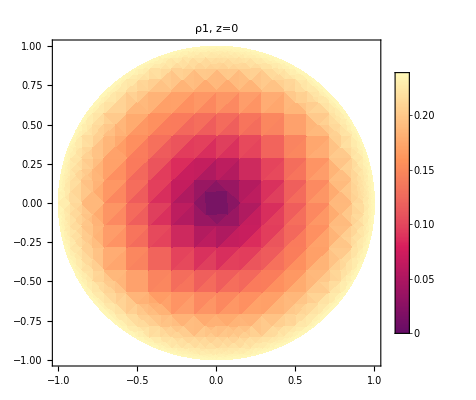

```mathematica
r0 = 1;
m0 = 1;

DensityPlot[
ρ1[x, y, 0] /. {m1->m0,r->r0},
{x, y} ∈ Disk[{0, 0}, r0],
PlotLabel->"ρ1, z=0",
PlotLegends->Automatic
]
```

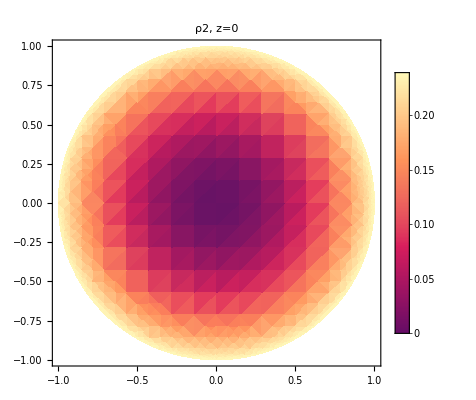

```mathematica
DensityPlot[
ρ2[x, y, 0] /. {m2->m0,r->r0},
{x, y} ∈ Disk[{0, 0}, r0],
PlotLabel->"ρ2, z=0",
PlotLegends->Automatic
]
```

### 5) Momenty bezwładności uzyskane dla gęstości odpowiednio , nazwij jako , ,

Dla zadanej masy oraz promienia kuli uszereguj to momenty od najmniejszego do największego.

```mathematica
inertiaValues = MapIndexed[
{inertiaFn, indexArr} |-> Module[{index, inertiaValue},
{index} = indexArr;
inertiaValue = inertiaFn /. {m -> m0, r -> r0};
"I" <> ToString[index - 1] -> inertiaValue
],
{I0, I1, I2}
];

Sort[
inertiaValues,
{a,b}|->a[[2]]<b[[2]]
]
```

{I0→2/5,I1→4/9,I2→10/21}

### 6) Dla rozkładu masy zadanego przez dla , gdzie jest liczbą naturalną, sprawdź przy jakim obliczony moment bezwładności niejednorodnej kuli różni się o mniej niż 1% od przypadku gdy cała masa będzie jednorodnie rozłożona na sferze o promieniu

```mathematica
ρn[n_][x_, y_, z_] := mn / (V r^n) * (x^2 + y^2 + z^2)^(n/2)

sphere = Sphere[centerOfMass, r];

inertiaOfSphere = m / Area[sphere] * MomentOfInertia[sphere, centerOfMass, directionVector]
```

(2 m r^2)/3

```mathematica
GetINPerDensity[n_] := CalculateBallInertia[ρn[n]]
GetINPerDensity[n]
```

(2 mn r^2)/(5+n)

```mathematica
GetBallMass[n_] := GetMassInDensityFunction[ρn[n]]
GetBallMass[n]
```

1/3 m (3+n)

```mathematica
GetBallIntertia[n_]:= GetINPerDensity[n] /. {mn -> GetBallMass[n]}
GetBallIntertia[n]
```

(2 m (3+n) r^2)/(3 (5+n))

```mathematica
RelativeInertiaDifference[n_] := Simplify[
Abs[GetBallIntertia[n] - inertiaOfSphere ] /inertiaOfSphere ,
Assumptions -> {n > 0, r > 0, m > 0}
]
RelativeInertiaDifference[n]
```

2/(5+n)

```mathematica
Reduce[RelativeInertiaDifference[n] < 1/100 && n >= 0, n]
```

n>195